```mathematica
Pattern[addition, {_,"+",_}]
```

addition:{_,+,_}

```mathematica
additionRules={__, "+",__}
```

{__,+,__}

```mathematica
MatchQ[{1, "+", 2}, additionRules]
```

True

```mathematica
commutativeGraph=[x, RelationGraph[commutativeAddition, {x,x}]][Range[100]](*Want to be able to define this functionally*)
```

```mathematica
commutativeGraph
```

commutativeGraph

```mathematica
MatchQ[1+2,2+1]
```

True

```mathematica
commutativeAddition[x_, y_]:=If[x+y==y+x, True, False]
```

```mathematica
algebra2PSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CK-12-Algebra-II-with-Trigonometry-Concepts_b_v78_eiy_s1.pdf", "Plaintext"]
```

1462420
 |  |  |  |

```mathematica
introAlgebraPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\scc_introductory_algebra_workbook_spring_2013.pdf", "Plaintext"];
```

```mathematica
calcPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CalcI_Complete_Problems.pdf", "Plaintext"]
```

Import::general: Expected cross reference table

Import::general: Could not find document trailer

General::stop: Further output of Import::general will be suppressed during this calculation.

```mathematica
a1QsPEMDAS={ "What is 2+2", "2+3","What is 2+3", "What is 1+1", "What is 20+22", "What is 1+15+21", "What is 33+5+8", "Simplify (2-5)^2", "Simplify 2-5^2", "Simplify 10-7+1", "Simplify 10-(7+1)", "Simplify 24/(4-2)^3", "Simplify 4+5(1+12/6)^2", "Simplify (15-3)/(1+5)", "1+12", "10% of 11", "30+40", "15+12", "20% of 33" , "11+12", "What is 5% of 100?"};
```

```mathematica
a1QsFractions={"express 3 2/7 as an improper fraction", "express 12 1/3 as an improper fraction", "Express 42/5 as a mixed number", "Express 53/9 as a mixed number", "write 3/18 in simplest form", "write 42/54 in simplest form" "What is 3 2/7 as an improper fraction","What is 12 1/3 as an improper fraction","What is 42/5 as a mixed number","What is 53/9 as a mixed number","What is 3/18 in simplest form","What is 42/54 in simplest form"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form"}
a1QsOppFrac={"Multiply 24/3 and 27/8", "Multiply 8 and 3/24", "Add 1/2 and 1/3", "What is  24/3 * 27/8", "What is  8 * 3/24", "What is  1/2 + 1/3"};
a1QsAbsoluteVal={"What is the absolute value of -1?", "What is |1|", "What is |-30|"};
a1QsNegatice={"What is 3-(-2)?", "What is -3+4"};
a1QsIntovars={"Evaluate a^2-b^2 when a=5 and b=3", "Evaluate a-b^2 when a=4 and b=2", "Evaluate a^2+b when a=7 and b=1"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form}

{Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form", }
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form,Null}

```mathematica
a1QsCombineLikeTerms={"Combine like terms of 3a-6a+10a-a", "Combine the like terms of 5x-10y+6z-3x", "Combine like terms of 3n-5n^2+6n-10+2n^2"};
```

```mathematica
a1QsDistrbutive={"5(2x+4)", "-3(x^2-2x+7)", "-(5x^4-8)"};
```

```mathematica
a1QsSolving={"8x-2=22", "-x-2=12", "2/3 x+3 =15"} ;
```

```mathematica
a1QsPolynomials={"Factor 3x^2+4x+1", "Factor n^2+5n+6", "Factor a^2+3a+2"};
```

```mathematica
a1QsPercent={"A $750 watch is on sale for 15% off. Find the sale price.", "A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?", "Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.", "A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.", 
"What is 10% of 100", "What is 4% of 16?", "200% of 3", "What is 45+300+4", "30+30", "90+200", "1+5", "34+1", "10% of 11", "5% of 112", "41+2" };
```

```mathematica
algebra1Questions=Flatten[{a1QsAbsoluteVal, a1QsCombineLikeTerms, a1QsDistrbutive, a1QsFractions, a1QsIntovars, a1QsPEMDAS, a1QsSolving, a1QsOppFrac, a1QsPercent, a1QsNegatice}];
```

```mathematica
algebra2PSetList[[8503;;8510]]
```

Part::take: Cannot take positions 8503 through 8510 in algebra2PSetList.

algebra2PSetList⟦8503;;8510⟧

```mathematica
algebra2Qs={"What is the most specific subset of the real numbers that -7 is a part of?", "Plot 1.25, 2/3 and 2 on a number line", "Identify the property used in the equations below as distributive, inverse or associative", "Evaluate 2x^2-9 for x=-3",  "Expand (a+b)^3", "What is (a+b)^n (Hint: What theorem is this?)", "Solve 4x-9=11", "Solve 3(x-5)+4=10", "Solve 3(x-5)+4=10", "Solve 9(x-3)+4=10", "Solve (x-1/2)=(2x+3)","Solve 3|x-5|=12","Solve 8(x-5)+4=10","Solve (x^2-5)=20",  "Use the law of sines to find the missing side of this triangle", "What is the largest value for the missing side of this triangle", "What is sin(60)", "What is tan(30)", "Write 30 degrees in radians", "Write π/4 in degrees", "Is x=-8 a solution to 1/2x+6>3?",  "Solve and graph the solution to 2x-3<7", "Solve and graph the solution to |3x-1|≥10",  "How many miutes are in a day?", "Wrie the standard form of y=3/2 x+2", "Write slope intercept form for a slope of 2 and y-intercept of 12", "Find a perpedicular line of y=3x+2 with y intercept of the origin","What are the domain and range of the trigonometric functions?" , "Graph the inequality y<3x+4", "Find the equation of best fit for the below listed data", "Graph the parabola give by x^2+3x+2. Find the zeros, vertex and intercept", "What is the sum from 1 to 5 of a=10n+3", "What is the next term in the series ", "what is the sum of the geometric series from 1 to infinity of 9(1/10)^n?", "What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?", "What is ln(1)?", "What are the domain and range of e^x and ln(x)", "sin(40)", "cos(45)", "tan(63)", "sin(121)", "sin(π/3)", "sin(π/5)", "cos(π/13)"};
```

```mathematica
calcQspcalc={"Evaluate f(x)=3-5x-2x^2 for the below values: f(0), f(x+h), f(6-t)", "Compute  the difrence quotient for the given function",  "Find the domain of (w^3-3w+1)/(12 w-7)","Find the inverse of f (x) = 6x +15", "Find inverse of W (x) =  (9 −11x)^(1/5)", "Find the exact value of cos(5 π/6) without using a calculator", "Find the exact value of sin(-4 π/3) without using a calculator", "Solve  4sin (3t ) = 2", "Solve 4sin (3t ) = 2 in [0, 4π/3], 2cos(x/3) +2^0.5 = 0 in [−7π ,7π }", "Solve 4y sec(7 y) = −21y", "Solve 3−14sin (12t + 7) =13", "Solve 3sec(4 − 9z) − 24 = 0", "Sketch the graph of f(x)=3^(1 + 2  x)", "Sketch the graph of h(x)=8+3e^(2  t - 4)",  "Determine ln(e^4)", "Combine 2 log_4x +5 log_4y - 1/2 log_4x" , "For the function W(x)=ln(1+x^4) and the point x=1, find the secants at point Q and the tangenet line", "For the function f(x)=(8-x^2)/(x^2-4), find the values at the below listed points and th limit as x aproaches 2",  , "For the function f(y)= sin(y)/y find the value at the below listed points and the limit as y approaches 0"};
```

```mathematica
calcQsderivs={"For the function f(x)=(8-x^2)/(x^2-4), use L'Hoptial's rule to find the limit as x aproaches 2",  "For the function (2-(t^2+3)^(1/2))/(t+1), L'Hoptial's rule to find the limit as x approaches -1", "Use the definition of the derivative to find the derivative of f(x)=6", "Use the definition of the derivative to find the derivative of V (t ) = 3−14t", 
 "Use the definition of the derivative to find the derivative of z(n)= (n+1)/(n+4)",
"Use the chain rule to find the derivative of Q(t)=(3t^3-4)^(1/2)", "Use the quotient rule to find the derivative of z(n)= (z+1)^(1/2)/(z+4)", 
"Find the deriviative of f (x) = 2cos(x) − 6sec(x) + 3", "Find the deriviative of g (z) =10 tan (z) − 2cot (z)", "Find the deriviative of  tan (w)sec(w)", "Find the deriviative of R(t)=(t+ tan(t))/(1+csc(t))", "Find the derivative of f(x)=2e^x-8^x", "Find the derivative of g(t)=4 log_3(t)-ln(t)", "Find the derivative of 2 cos(x)+arccos(x)" , "Find the derivative of x^2/y^3=1", "Find extrema of f(x)=12+6x^2-x^3", "Find extrema of g(w)=tan (w)sec(w)", "find the taylor expanision of g(w)=tan (w)sec(w) at w=π/4", "Find the MacLauren Expanision of z(n)= (z+1)^(1/2)/(z+4)", "Find the Derivative", "What is the Deriviative", "Evaluate the derivative", "Integral of ln(x) dx", "Integral of f(x)=x ln(x) from 0 to 10", "Integral of tan(x)", "Integral of (1+x)^(1/2)"};
```

```mathematica
calcQsIntegral={"Find ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7", "Evaluate ∫z^6 + 4z^4 − z^2 dz" ,"Determine f (x) given that f'(x) = 6x^8 − 20x^4 + x^2 + 9", "Find ∫ 2cos (w) − sec(w) tan (w)dw", "Find ∫12 + csc(θ ) [sin (θ ) + csc(θ )] dθ",
"What is ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7",
"What is the integral of sin(2x)?", "Find the area under the curve of |x| from -1 to 1", "What is the area under the curve sin^2x from 0 to π/2", "Find the integral", "What is the integral of x dx", "Derivative of f(x)=x^2", "Integral of x dx", "Integral of e^y dy", "Derivative of x^3", "Derivative of x", "Derivative of f(x)=20 ln(x)", "Derivative of x/(x+1)^2", "Derivative of x^n", "Derivative with respect to x", "Derivative of x^3"};
```

```mathematica
calcQs=Flatten[{calcQspcalc, calcQsIntegral, calcQsderivs}];
```

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs, "calc"->calcQs|> , Method->"NaiveBayes", PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
equivilentFraction[x_, y_, n_]:= n*x/y ;
turnOffEquivFrac[question_]:=MatchQ[question, {__, "Fraction",__,"implest form"}]
Function[question,MatchQ[question,{"Fraction",__,"implest form"}]]
allpoints[question_]:=MatchQ[question, {__, "all points", __}]
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d")"}}-> {{"("c, d")"},{"(",a, b, ")"}}
isPoint[answer_]:=MatchQ[answer, {"("__")"}]
commutative[a_,b_]:=a+b-> b+a
distributive[a_,b_, c_]:=a*(b+c)-> a*b+a*c
commutativemulti[a_, b_]:=a*b-> b*a;
associative[a_, b_, c_]:=a+(b+c)-> (a+b)+c;
associativemulti[a_, b_,c_]:=a*(b*c)-> (a*b)*c;
isMatrix[answer_]:=MatchQ[answer, MatrixForm]
```

Function[question,MatchQ[question,{Fraction,__,implest form}]]

Classify::bdfmt: Argument «1» should be a rule, a list of rules, or an association.

Classify::bdfmt: Argument … should be a rule, a list of rules, or an association.

ClassifierFunction[…]

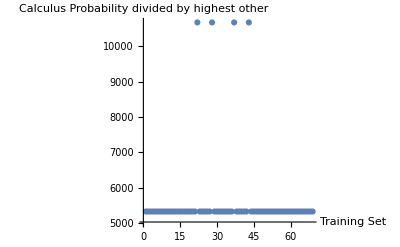

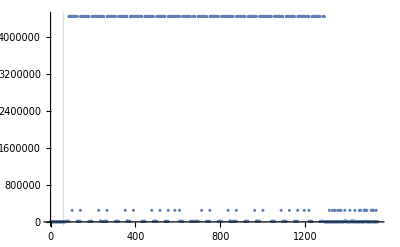

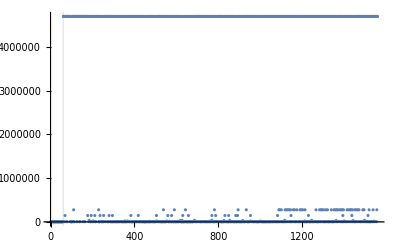

C:\Users\Silas Grossberndt\Documents\GitHub\WSS-Template\Final Project\Drafts\problem_sets\pset_trained_NaiveBayes.pdf

```mathematica
calctsetlist=questionClassifier[calcQs, {"Probability", "calc"}];

algebra1calctsetlist=questionClassifier[calcQs, {"Probability", "algebra 1"}];
algebra2calctsetlist=questionClassifier[calcQs, {"Probability", "algebra 2"}];
lp=ListPlot[#clac/#alge, AxesLabel->{"Training Set", "Calculus Probability divided by highest other"}]&@<|"clac"->calctsetlist, "alge"->algebra1calctsetlist, "alge2"-> algebra2calctsetlist|> 
a2tsetlist=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}];

ca2tsetlist=questionClassifier[algebra2Qs, {"Probability", "calc"}];

a1a2tsetlist=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}];
a1tsetlist=questionClassifier[algebra1Questions, {"Probability", "algebra 1"}];
ca1tsetlist=questionClassifier[algebra1Questions, {"Probability", "calc"}];
lp1=ListPlot[#alge1/#calc1, GridLines->{{0, 60, 1}}]&@<| "alge1"->a1tsetlist, "calc1"->ca1tsetlist|> 
lp2=ListPlot[#alge2/#calc1, GridLines->{{0, 60, 1}}]&@<| "alge2"->a2tsetlist, "calc1"->ca2tsetlist, "alge1"-> a1a2tsetlist|> 
Export["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\pset_trained_NaiveBayes.pdf", {lp, lp1, lp2}]
```

```mathematica
"C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\pset_trained_.pdf"
```

C:\Users\Silas Grossberndt\Documents\GitHub\WSS-Template\Final Project\Drafts\problem_sets\pset_trained_.pdf

```mathematica
(*include the above graphs and the test functions to show infeasiability of doing the classifier*)

questionClassifier["Derivative of f(x)=x^2"]
questionClassifier["Integral of x dx"]

questionClassifier["What is 10% of 110", {"Probabilities"}]

questionClassifier["sin(π/5)"]
(*Need to add more training about sine to a2, derivative to calc*)

questionClassifier["35+3"]
questionClassifier["Derivative of f(x)=x^6"]
ClassifierMeasurements[questionClassifier, <|"algebra 1"-> algebra1Questions,"algebra 2"-> algebra2Qs, "calc"-> calcQs|>, "Accuracy"]
```

calc

calc

{<|algebra 1→0.486282,algebra 2→0.491643,calc→0.0220751|>}

algebra 2

algebra 2

algebra 2

0.715593

```mathematica
wpgRadicals=StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\WolframProblemGenerator-RadicalSummaryQuizKey.pdf", "Plaintext"]]
```

Import::general: Could not find the start of the cross reference table

Import::general: Expected cross reference table

Import::general: Could not find the start of the cross reference table

General::stop: Further output of Import::general will be suppressed during this calculation.

{}

```mathematica
wpgRadicals
```

{}

```mathematica
algebra2set=StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\algebra_2_set.pdf", "Plaintext"], {".)", "\n"}];
algebra2set[[2;;20;;7]]
```

{    9 + 3x + 7x = 39  \r,    - 6 + x + x = 14  \r,    - 5x + 7 + 6x = 18  \r}

```mathematica
AppendTo[algebra2Qs, algebra2set⟦2;;-1;;7⟧];
```

{What is the most specific subset of the real numbers that -7 is a part of?,Plot 1.25, 2/3 and 2 on a number line,Identify the property used in the equations below as distributive, inverse or associative,Evaluate 2x^2-9 for x=-3,Expand (a+b)^3,What is (a+b)^n (Hint: What theorem is this?),Solve 4x-9=11,Solve 3(x-5)+4=10,Solve 3(x-5)+4=10,Solve 9(x-3)+4=10,Solve (x-1/2)=(2x+3),Solve 3|x-5|=12,Solve 8(x-5)+4=10,Solve (x^2-5)=20,Use the law of sines to find the missing side of this triangle,What is the largest value for the missing side of this triangle,What is sin(60),What is tan(30),Write 30 degrees in radians,Write π/4 in degrees,Is x=-8 a solution to 1/2x+6>3?,Solve and graph the solution to 2x-3<7,Solve and graph the solution to |3x-1|≥10,How many miutes are in a day?,Wrie the standard form of y=3/2 x+2,Write slope intercept form for a slope of 2 and y-intercept of 12,Find a perpedicular line of y=3x+2 with y intercept of the origin,What are the domain and range of the trigonometric functions?,Graph the inequality y<3x+4,Find the equation of best fit for the below listed data,Graph the parabola give by x^2+3x+2. Find the zeros, vertex and intercept,What is the sum from 1 to 5 of a=10n+3,What is the next term in the series ,what is the sum of the geometric series from 1 to infinity of 9(1/10)^n?,What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?,What is ln(1)?,What are the domain and range of e^x and ln(x),sin(40),cos(45),tan(63),sin(121),sin(π/3),sin(π/5),cos(π/13),{    9 + 3x + 7x = 39  \r,    - 6 + x + x = 14  \r,    - 5x + 7 + 6x = 18  \r,    2x - 5 + 7x = 85  \r,    2 = 3x + 7x + 2  \r,    - x - 6 + 2x = - 11  \r,    - 5x + 4 + 2x = 25  \r,    9 + 6x + 4x = 29  \r,9,10,11,12,13,14,15,16, \r, \r, \r, \r, \r, \r, \r,    - 2x +  /  = - 7x +    /   \r,\r, \r, \r, \r, \r, \r, \r, \r, \r,8      8    6\r,33, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    2x - 7 = 4x -    /   \r,-23      3\r, \r, \r, \r,3       2      6\r,    9 - 5x = - 6x - 2  \r,    - 7x + 10 = - x + 4  \r,    - 4x + 7 = 6x - 83  \r,197     3\r, \r, \r, \r, \r, \r, \r,2\r,    3 - 6x = 7x - 36  \r,58\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    - 5 + 5x = 3x -    /   \r,77, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,9                    9\r,89, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,101, \r, \r, \r, \r, \r, \r, \r, \r,    4x + 10 = 5x + 5  \r,110, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r,    - 5(3 + 6x) =     /   \r,3\r, \r, \r, \r, \r, \r, \r,    - 6(8 + x) =      /   \r,137,138,\r, \r, \r, \r, \r, \r, \r, \r,    5( /3x + 1) =    /3  \r,147,1\r, \r, \r, \r, \r, \r, \r,\r, \r, \r,    - 5( - 4 +  / x) =  /   \r,158,4            -440\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,2\r,    7(-1x + 4) = 91  \r,    7( - 8 + 4x) = 84  \r,    7(3x + 2) = 266  \r,175, \r, \r,\r, \r, \r, \r, \r, \r,    6(  /  + 7x) = - 44  \r,184,-1               381\r, \r, \r, \r, \r, \r,      / (4x -  / ) =      /     \r,191,192,\r, \r, \r, \r, \r, \r, \r,    2(4x -  / ) =    /   \r,200, \r, \r, \r, \r, \r, \r, \r, \r, \r,    4(7x + 4) = 128  \r,210, \r, \r, \r, \r,     / (  /  - 7x) =     /     \r,215,\r, \r, \r, \r, \r, \r, \r, \r,       - 5x - 4y = - 39  \r,224, \r, \r, \r,       - 2x - y = - 17  \r,    4x + y = - 7 \r,229,\r, \r, \r, \r,       - 2x - y = - 13  \r,234, \r, \r,     / x - 2y =      /    \r, \r,9\r, \r, \r,3              3\r,240, \r, \r,      / x + 4y =     /  \r, \r,      2x + 4y =    /   \r,244, \r, \r, \r,      5x + y = 40  \r,248, \r, \r,250, \r, \r,    3x + 4y =      /  \r, \r, \r, \r,       - 3x - 2y = 5  \r,    4x + 2y = 50 \r, \r, \r, \r, \r, \r,     / x +  / y =     /  \r, \r, \r,       - 2x + 5y = 15  \r,    2x + 5y = 28 \r,265, \r, \r, \r,      5x - 4y = 68  \r,269, \r,    4x + 3y =     /  \r, \r,2                      -26\r, \r, \r,       / x - y =    /     \r,1\r, \r,      x - 2y = - 5  \r,1             -271\r, \r,      x - 5y = - 35  \r,    - 5x + 3y = - 8 \r,279, \r, \r, \r,      - x + 5y = 30  \r,1\r, \r, \r, \r,    x -  / y = - 7 \r, \r, \r, \r, \r,      2x - 4y = - 24  \r,291, \r, \r,    3x -  / y =     /  \r, \r, \r,\r, \r,      5x + y = 11  \r,    x + 4y = 28 \r,-51\r, \r,    3x + 2y =     /  \r, \r,79\r, \r,      2x + 4y =     /   \r,303, \r, \r, \r,1                     -23\r, \r, \r, \r,       - 4x +  / y =     /   \r,310, \r,5              5\r,    4x + 2y = - 16 \r,313, \r, \r,-37\r, \r, \r, \r, \r, \r,      2x - 3y = 19  \r,    2x + 4y = 0 \r,\r, \r, \r,      5x - y = - 17  \r,325, \r, \r,1             -575\r, \r, \r, \r,       / x - 3y =     /   \r,331, \r, \r, \r,      / x + 2y =  /  \r, \r, \r,       - 5x - 2y = 8  \r,    2x + y = - 6 \r,338, \r, \r, \r, \r,      4x + y = 20  \r,    4x + 4y = 4 \r,344, \r,       - 2x + y = 1  \r,    - 3x + y = - 31 \r,347, \r,10\r,83\r, \r,      2x + 5y = 21  \r,351, \r, \r,       - 2x + 5y = 23  \r,    - 5x + y = 27 \r, \r, \r, \r, \r,       - 4x +  / y = 4  \r,-41\r, \r,     / x - 2y = - 28 \r, \r,       - 2x - y =     /   \r, \r,4\r,    2x + 4y = - 8 \r,364, \r, \r,       - 3x +  / y = - 24  \r,367, \r, \r, \r, \r,    - x + y =    /  \r, \r, \r, \r,      - x + 2y = 21  \r,375, \r, \r, \r,      5x - 2y = - 47  \r,    - 4x - y = - 23 \r,380, \r, \r,     / x -  / y = - 2 \r, \r,      x + 2y = 21  \r,384, \r,5         5\r,386, \r,\r, \r,7\r, \r, \r,2      18\r, \r, \r, \r, \r,      / x + 2y = - 5 \r, \r, \r, \r,      / x + y =  /  \r, \r, \r,5            5\r, \r, \r,       - 4x +  / y =    /   \r,403, \r, \r,      x - y =    /   \r,4            29\r, \r, \r,    2x + 5y = - 22 \r,-13\r, \r,    5x - y =     /  \r, \r,2\r,    4x + 3y = - 17 \r,413, \r, \r,-3\r, \r, \r,      3x + 4y =     /   \r,418, \r, \r,5        10\r,421, \r, \r,7\r, \r, \r, \r, \r,\r,428, \r, \r,       / x - y =     /   \r,431, \r, \r,5         5\r, \r, \r,      4x - 3y =     /   \r,436, \r, \r, \r,      3x -  / y = - 23  \r,13\r,\r,    - 5x + 3y = 36 \r, \r, \r, \r, \r,    - 4x + 2y =     /  \r, \r, \r,      5x - 4y = - 39  \r,    3x + 5y = 61 \r,449, \r,2\r,451, \r, \r,    2x +  / y =    /  \r, \r,       / x - 5y = - 10  \r,455, \r, \r,3           21\r, \r, \r,      4x + 3y = 43  \r,3                        -27\r, \r,11\r,462, \r, \r, \r,      3x + 3y = 24  \r,    - x + 5y = 44 \r, \r, \r, \r,-1\r, \r,5\r,    2x + 3y = - 20 \r,472, \r, \r,      3x - 5y = - 31  \r,    2x - 2y = 2 \r,476, \r,5\r,    2x - y = - 28 \r,479,\r, \r,      2x - y = - 22  \r,    2x - 4y = 18 \r,3             -33\r, \r,4              4\r,    - 2x - 2y = - 28 \r,-3             123\r, \r, \r,    5x -  / y = 24 \r, \r,2\r, \r, \r, \r,       - 2x + 2y = 16  \r,493, \r,      x + y = 7  \r,    4x - 3y = - 7 \r,496, \r,3      58\r, \r, \r,\r,       / x + y =    /   \r,501, \r, \r, \r,      3x + y = - 8  \r,505, \r,      4x - 2y = - 8  \r,    2x - y = - 3 \r,-24\r, \r,     / x + y = - 2 \r, \r, \r, \r,      5x - 4y = 30  \r,-173\r, \r,      x + 5y = 51  \r,    - 4x + y = - 10 \r,516, \r, \r,1                         -8\r, \r, \r, \r,3\r, \r, \r, \r, \r,       - 4x + 4y = 68  \r,526, \r, \r, \r,1             -33\r, \r, \r, \r,-62\r, \r, \r, \r, \r,    3x +  / y =    /  \r, \r, \r, \r,2              2\r, \r, \r, \r, \r,      6x + 3y = 69  \r,544, \r, \r,    x + 4y = 49 \r,547, \r, \r, \r,165\r, \r, \r,-93\r, \r, \r, \r,9             3\r, \r, \r, \r, \r,      - x + 8y = 18  \r,    - 3x - y = 1 \r,561, \r, \r, \r,    3x +  /4y =     /4 \r, \r, \r,       / x + 4y = 8  \r,-80\r, \r,    4x + 2y =     /  \r, \r, \r, \r,      9x - 5y = 41  \r,572, \r, \r, \r,5         5\r,576, \r, \r,236\r, \r,      4x - 10y =  /   \r,580, \r, \r, \r, \r,3\r,\r, \r, \r,185\r, \r, \r,       / x -  / y =   /   \r,590, \r, \r,-2                            -32\r, \r,2\r,    5x - 5y = - 70 \r,595, \r, \r, \r,\r, \r,      6x + 3y =      /   \r,-1\r, \r, \r,5              5\r, \r, \r,       - 2x + 20y = - 20  \r,    x + y = 4 \r,2      91\r, \r,    5x +  / y =  /  \r, \r, \r, \r, \r, \r,612, \r, \r, \r,5        5\r, \r, \r, \r,       - 3x + 12y = - 9  \r,    - x - 5y = - 57 \r,-53\r, \r,       - 3x + 3y = 21  \r,    5x + 2y = - 31 \r,623, \r, \r, \r,       - 4x -  / y =     /   \r,627, \r,5\r,    2x + y = 12 \r, \r, \r,\r,632, \r, \r, \r,    2x - 4y =     /  \r, \r, \r, \r,638, \r, \r,     / x - y =   /  \r, \r,5             15\r,    - 5x - 4y = - 67 \r,2                         -74\r, \r,\r,    2x + 2y = 18 \r,2             23\r, \r, \r,3\r, \r, \r, \r,       - 3x - y = 15  \r,    3x + 5y = 15 \r,653, \r, \r, \r, \r, \r,    5x + 2y = 50 \r, \r, \r, \r, \r,       - 4x + 4y = 4  \r,663, \r,    - 3x - y =     /  \r, \r,      2x - 5y = 35  \r,666, \r, \r,      5x - 5y = 45  \r,    5x + 5y = 6 \r, \r,\r, \r,       - 2x - 3y = 7  \r,    2x + 5y = 70 \r,674, \r, \r, \r,\r,678, \r,2\r,680, \r, \r,    2x + 2y =    /  \r, \r,1      442\r, \r, \r,       - 5x + 3y =     /   \r,686, \r, \r,        / x - y =  /     \r,689, \r,5         35\r,3      3             -18\r, \r,224\r, \r, \r,5\r, \r, \r, \r,      - x - 5y = 24  \r,    2x + 3y = 6 \r,3      63\r, \r, \r, \r,      4x + 3y = 55  \r,    x + 3y = 5 \r, \r, \r, \r, \r, \r,2\r, \r, \r, \r,       / x + 2y =     /   \r,712, \r, \r,      5x +  / y = - 48  \r,715, \r, \r, \r,      x + 5y =     /   \r,37\r, \r,4             -184\r, \r, \r, \r,\r,1\r, \r, \r, \r,    2x = - 4y +     /    \r, \r, \r, \r,730, \r, \r, \r,2             3\r, \r, \r,      x +  / y =     /     \r,736, \r, \r, \r, \r,    x = - 2y +     /    \r, \r, \r, \r,    y = - 2x + 19 \r,744, \r, \r, \r,24\r,748, \r, \r,      y = - x - 2  \r,    - 2y + 4x = 20 \r,752, \r, \r,       - 2x =      /  + 3y  \r,755, \r, \r, \r,4\r, \r, \r, \r,4\r, \r,      x +  /2y =   /2  \r,41\r, \r,      y = - 5x - 18  \r,765, \r, \r, \r, \r,      2y - x = - 16  \r,770, \r,28    4\r,    x = 2y + 9 \r,773, \r, \r,      x = - y +    /   \r, \r, \r,      5x + 4y =     /   \r,778, \r,5       5\r,780, \r, \r,    x =   / y -  /  \r, \r, \r,    - x = 5y +     /  \r, \r, \r, \r,      x = - 5y - 8  \r,788, \r,1       2             -11\r, \r, \r, \r,      x = y + 4  \r,    y - x = 2 \r,794, \r, \r,    - 3x = - 3y - 39 \r,797, \r, \r, \r,2      53\r, \r, \r, \r, \r,      4y + x = 22  \r,    y = - 5x - 9 \r,806, \r, \r, \r,3              3\r,810, \r, \r, \r, \r, \r,-2      14\r, \r,      x =   / y +  /   \r,817, \r, \r, \r,       - 2x + 4y = - 18  \r,821,\r, \r, \r, \r,    x  + 13x + 12 = 0  \r,826,2\r, \r, \r, \r,    x  +     / x +    /  = 0  \r,2\r, \r, \r, \r, \r,    x  + 0x - 16 = 0  \r,836,2\r, \r, \r, \r,    x  - 10x + 24 = 0  \r,841, \r, \r, \r, \r,    x  - 19x + 88 = 0  \r,846,2  13       4\r, \r, \r, \r,3\r,851,2\r, \r, \r, \r,    x  - 20x + 96 = 0  \r,856,2\r, \r, \r, \r, \r,861,2\r, \r, \r, \r, \r, \r,    x  - 3x - 108 = 0  \r,2\r, \r, \r, \r, \r,    x  - 6x + 0 = 0  \r,873,2\r, \r,\r, \r, \r,    x  + 3x + 0 = 0  \r,879, \r, \r, \r, \r, \r,884,2\r, \r, \r, \r, \r,    x  -    / x + 4 = 0  \r,2\r, \r, \r, \r,3      3\r,894, \r, \r, \r, \r,    x  - 15x + 50 = 0  \r,2\r, \r, \r, \r, \r, \r, \r,    x  + 4x - 60 = 0  \r,906, \r, \r, \r, \r,    x  - 12x + 0 = 0  \r,911,2\r, \r, \r, \r, \r,    x  -    / x +    /  = 0  \r,2\r, \r, \r, \r, \r, \r,922,2\r, \r, \r, \r, \r,      / x  -     / x + 2 = 0  \r,2   37      4\r, \r, \r,7\r,931,2\r, \r, \r, \r,7        7\r,936,-3   2   287        2\r, \r, \r,    x  + 26x + 48 = 0  \r,940, \r, \r, \r, \r,      / x  - x + 36 = 0  \r,\r, \r, \r, \r,    - 24x  + 58x + 16 = 0  \r,949,2    73        21\r, \r, \r, \r,    - 24x  - 20x + 24 = 0  \r,954, \r, \r, \r,3\r,958, \r, \r, \r, \r,    28x  - 56x + 28 = 0  \r,963,8   2\r, \r, \r, \r, \r,968, \r, \r, \r, \r, \r,    12x  - 46x - 8 = 0  \r,974,2\r, \r, \r, \r, \r,    - 8x  - 14x + 4 = 0  \r,980,2   122\r, \r, \r, \r,984,36   2   318\r, \r, \r, \r,    - 2x  -     / x - 18 = 0  \r,2\r, \r, \r, \r, \r,    - 35x  + 53x - 20 = 0  \r,994,2\r, \r, \r, \r, \r,999,2\r, \r, \r, \r, \r,    56x  + 23x + 2 = 0  \r,1005,2\r, \r, \r, \r,    12x  - 11x - 15 = 0  \r,1010,2    61       3\r, \r, \r, \r,1014,2\r, \r, \r, \r, \r,    25x  - 30x - 7 = 0  \r,1020,2\r, \r, \r, \r, \r,    - 5x  + 13x - 8 = 0  \r,1026,2   1\r, \r, \r, \r,1030, \r, \r, \r, \r,    5x  + 12x + 4 = 0  \r,1035,2\r, \r, \r, \r, \r,    7x  + 14x + 7 = 0  \r,1041,2         1\r, \r, \r, \r,    - x  + 8x + 9 = 0  \r,1046,2\r, \r, \r, \r, \r,    - 12x  + 10x -  /  = 0  \r,2\r, \r, \r, \r,5\r,1056,2\r, \r, \r, \r,1060,2\r, \r, \r, \r, \r, \r,    8x  + 13x + 5 = 0  \r,1067, \r,2\r, \r, \r, \r, \r, \r,    - 10x  +  / x + 11 = 0  \r,2\r, \r, \r, \r,    - x  - 4x + 8 = 0  \r,1079,2\r, \r, \r,\r,    7x  - 10x + 1 = 0  \r,1084,2\r, \r, \r, \r,7\r,1089, \r, \r, \r, \r,    8x  + 13x + 5 = 0  \r,1094, \r, \r, \r,    - 3x  - 2x + 4 = 0  \r,1098,2\r, \r, \r, \r, \r, \r,1104,2\r, \r, \r, \r, \r, \r,    - 6x  + 4x + 7 = 0  \r,2\r, \r, \r, \r,        / x  -  / x + 8 = 0  \r,2\r, \r, \r, \r,\r,1119,2\r, \r, \r, \r,5\r,1124, \r, \r, \r,    2x  + 9x + 11 = 0  \r,1128,2\r, \r, \r, \r, \r,    9x  - 8x + 11 = 0  \r,1134,2\r, \r, \r, \r, \r, \r,1140,2\r, \r, \r, \r, \r, \r,    6x  + 2x + 8 = 0  \r,2\r, \r, \r, \r, \r, \r,    3x  - 12x + 13 = 0  \r,1153, \r, \r, \r,     / x  + 9x + 25 = 0  \r,3   2\r, \r, \r, \r, \r,    11x  + 4x + 11 = 0  \r,2\r, \r, \r, \r,11\r,1166,2\r, \r, \r,3\r,1170, \r, \r, \r, \r,    5x  + 10x + 6 = 0  \r,1175, \r, \r, \r, \r, \r,    8x  + 10x + 9 = 0  \r,1181, \r,\r, \r, \r,    4x  + 7x + 4 = 0  \r,1186,2\r, \r, \r, \r,    7x  - 11x + 5 = 0  \r,1191,2   7\r, \r, \r, \r, \r,    6x  + 12x + 7 = 0  \r,3   2\r, \r, \r, \r, \r,    8x  - 3x + 2 = 0  \r,1202,2\r, \r, \r, \r,11\r,1207, \r, \r, \r, \r, \r,1212, \r, \r, \r, \r, \r,    4x  - 7x +    /  = 0  \r,2\r, \r, \r, \r}}

```mathematica
algebra2Qs=Flatten[algebra2Qs]; (*Algebra 2 eats eaverything now, but this is good, can do for the rest of the types*)
```

```mathematica
algebra1set:=StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\algebra_1_set.pdf", "Plaintext"], {".)",  "\n"}];
```

```mathematica
settoappend=algebra1set⟦2;;-1;;7⟧;
```

```mathematica
AppendTo[algebra1Questions, settoappend];
```

```mathematica
algebra1Questions=Flatten[algebra1Questions];
```

```mathematica
AppendTo[algebra1Questions, StringSplit[Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\Maths Question Generator.pdf", "Plaintext"], "\n"]];
```

{What is the absolute value of -1?,What is |1|,What is |-30|,Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2,5(2x+4),-3(x^2-2x+7),-(5x^4-8),express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form,Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1,What is 2+2,2+3,What is 2+3,What is 1+1,What is 20+22,What is 1+15+21,What is 33+5+8,Simplify (2-5)^2,Simplify 2-5^2,Simplify 10-7+1,Simplify 10-(7+1),Simplify 24/(4-2)^3,Simplify 4+5(1+12/6)^2,Simplify (15-3)/(1+5),1+12,10% of 11,30+40,15+12,20% of 33,11+12,What is 5% of 100?,8x-2=22,-x-2=12,2/3 x+3 =15,Multiply 24/3 and 27/8,Multiply 8 and 3/24,Add 1/2 and 1/3,What is  24/3 * 27/8,What is  8 * 3/24,What is  1/2 + 1/3,A $750 watch is on sale for 15% off. Find the sale price.,A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?,200% of 3,What is 45+300+4,30+30,90+200,1+5,34+1,10% of 11,5% of 112,41+2,What is 3-(-2)?,What is -3+4,    x / - 5 = - 3  \r,    x / 6 = 5  \r,    x + 4 = 16  \r,    x + 6 = 8  \r,    x + 9 = 13  \r,    2 = x - 3  \r,    x - 1 = - 10  \r,    x + 4 = - 4  \r,9,10,11,12,13,14,15,16, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    - 7 + x = 2  \r,    x / 3 = 3  \r,    13 = x + 1  \r,    x + 8 = 12  \r,    x + 6 = 6  \r,    4x = - 44  \r,    x / 4 = 7  \r,    x + 8 = 3  \r,63,64,65,66,67,68,69,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    x + 4 = - 6  \r,    - 9 + x = - 5  \r,    6x = - 48  \r,    15 = x + 4  \r,    11 = x + 10  \r,    x - 2 = - 8  \r,    10 + x = 1  \r,116,117,118,119,120,121,122,123, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r,    7x = 0  \r,    7 + x = 13  \r,    - 3 = x + 2  \r,    x / 6 = 6  \r,    x / - 2 = 1  \r,    x + 2 = 3  \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    x / 7 = 2  \r,    3 = x + 3  \r,    x + 2 = - 8  \r,    x + 5 = -1  \r,    x + 7 = 13  \r,    -1 + x = -1  \r,    12 = x + 7  \r,    x + 8 = 14  \r,186,187,188,189,190,191,192,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    x + 2 = 8  \r,    x + 7 = 18  \r,    x + 9 = 2  \r,    - 5x = - 10  \r,    x - 4 = 0  \r,    x - 2 = 3  \r,    - 9 + x = - 7  \r,239,240,241,242,243,244,245,246, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r,    x + 10 = 12  \r,    7 + x = 13  \r,    2x = 2  \r,    - 3 = x - 4  \r,    - 10 + x = 1  \r,    18 = x + 8  \r,    5 + x = 12  \r,    x - 5 = 7  \r,293,294,295,296,297,298,299,300, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    4x - 8 = 8  \r,    5x + 5 = 10  \r,    - 4x + 9 = - 27  \r,    10 + 5x = 10  \r,    6x - 3 = - 75  \r,    8 + 2x = 14  \r,    4x + 7 = 15  \r,362,363,364,365,366,367,368,369, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r,    10 + 5x = 60  \r,    - 5x - 2 = - 27  \r,    6x - 5 = 67  \r,    - 7x - 5 = - 26  \r,    7 - 7x = 63  \r,    7x + 6 = - 78  \r,    - 8 - 7x = 62  \r,    5x + 9 = -1  \r,416,417,418,419,420,421,422,423, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    5x - 9 = - 19  \r,    5x + 7 = - 33  \r,    6x + 7 = 25  \r,    3x - 6 = - 6  \r,    4 + 6x = 16  \r,    - 5 + 7x = 79  \r,    - 5x + 8 = 28  \r,    2x - 7 = 13  \r,470,471,472,473,474,475,476,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r,    2x + 8 = 10  \r,    3 - 3x = - 30  \r,    - 8 - 5x = 17  \r,    2x + 5 = - 7  \r,    3 + 4x = - 45  \r,    3x + 7 = 25  \r,    - 5x + 5 = 25  \r,537,538,539,540,541,542,543, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    9 - 3x = - 21  \r,    4x - 9 = 19  \r,    6x + 1 = 61  \r,    - 2x + 8 = 32  \r,    10 + 3x = 10  \r,    2 - 2x = - 22  \r,    8 + 5x = 48  \r,587,588,589,590,591,592,593, \r, \r, \r, \r, \r, \r, \r,    x / - 5 = - 3  \r,    x / 6 = 5  \r,    x + 4 = 16  \r,    x + 6 = 8  \r,    x + 9 = 13  \r,    2 = x - 3  \r,    x - 1 = - 10  \r,    x + 4 = - 4  \r,9,10,11,12,13,14,15,16, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    - 7 + x = 2  \r,    x / 3 = 3  \r,    13 = x + 1  \r,    x + 8 = 12  \r,    x + 6 = 6  \r,    4x = - 44  \r,    x / 4 = 7  \r,    x + 8 = 3  \r,63,64,65,66,67,68,69,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    x + 4 = - 6  \r,    - 9 + x = - 5  \r,    6x = - 48  \r,    15 = x + 4  \r,    11 = x + 10  \r,    x - 2 = - 8  \r,    10 + x = 1  \r,116,117,118,119,120,121,122,123, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r,    7x = 0  \r,    7 + x = 13  \r,    - 3 = x + 2  \r,    x / 6 = 6  \r,    x / - 2 = 1  \r,    x + 2 = 3  \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    x / 7 = 2  \r,    3 = x + 3  \r,    x + 2 = - 8  \r,    x + 5 = -1  \r,    x + 7 = 13  \r,    -1 + x = -1  \r,    12 = x + 7  \r,    x + 8 = 14  \r,186,187,188,189,190,191,192,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    x + 2 = 8  \r,    x + 7 = 18  \r,    x + 9 = 2  \r,    - 5x = - 10  \r,    x - 4 = 0  \r,    x - 2 = 3  \r,    - 9 + x = - 7  \r,239,240,241,242,243,244,245,246, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r,    x + 10 = 12  \r,    7 + x = 13  \r,    2x = 2  \r,    - 3 = x - 4  \r,    - 10 + x = 1  \r,    18 = x + 8  \r,    5 + x = 12  \r,    x - 5 = 7  \r,293,294,295,296,297,298,299,300, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    4x - 8 = 8  \r,    5x + 5 = 10  \r,    - 4x + 9 = - 27  \r,    10 + 5x = 10  \r,    6x - 3 = - 75  \r,    8 + 2x = 14  \r,    4x + 7 = 15  \r,362,363,364,365,366,367,368,369, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r,    10 + 5x = 60  \r,    - 5x - 2 = - 27  \r,    6x - 5 = 67  \r,    - 7x - 5 = - 26  \r,    7 - 7x = 63  \r,    7x + 6 = - 78  \r,    - 8 - 7x = 62  \r,    5x + 9 = -1  \r,416,417,418,419,420,421,422,423, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    5x - 9 = - 19  \r,    5x + 7 = - 33  \r,    6x + 7 = 25  \r,    3x - 6 = - 6  \r,    4 + 6x = 16  \r,    - 5 + 7x = 79  \r,    - 5x + 8 = 28  \r,    2x - 7 = 13  \r,470,471,472,473,474,475,476,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,\r,    2x + 8 = 10  \r,    3 - 3x = - 30  \r,    - 8 - 5x = 17  \r,    2x + 5 = - 7  \r,    3 + 4x = - 45  \r,    3x + 7 = 25  \r,    - 5x + 5 = 25  \r,537,538,539,540,541,542,543, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r, \r,    9 - 3x = - 21  \r,    4x - 9 = 19  \r,    6x + 1 = 61  \r,    - 2x + 8 = 32  \r,    10 + 3x = 10  \r,    2 - 2x = - 22  \r,    8 + 5x = 48  \r,587,588,589,590,591,592,593, \r, \r, \r, \r, \r, \r, \r,{9 + 17 \r,0 + 90 \r,88 + 4 \r,6 + 48 \r,58 + 1 \r,8 + 53 \r,0 + 38 \r,60 + 0 \r,89 + 4 \r,4 + 26 \r,70 + 1 \r,26 + 3 \r,1697 + 7259 \r,4988 + 7311 \r,2521 + 8308 \r,1451 + 9116 \r,6101 + 5023 \r,6427 + 5512 \r,9831 + 9261 \r,5365 + 2334 \r,2269 + 7414 \r,7505 + 3155 \r,1713 + 5630 \r,\r,3047 + 3011 \r,2278 + 3852 \r,4189 + 2776 \r,8853 - 4648 \r,2026 + 3727 \r,0.8 .00.99 4 \r,6591 + 6757 \r,0.8 .00.99 0.46 \r,5322 - 1144 \r,0.55 .00.99 9 \r,8636 - 4683 \r,0.47 .00.99 0.2 \r,8691 ʹ  1618 \r,\r,18 + 6 \r,12 + 8 \r,7 + 90 \r,18 + 4 \r,2 + 63 \r,35 + 2 \r,1 + 80 \r,7 + 92 \r,20 + 8 \r,\r,41 + 6 \r,47 + 5 \r,30 + 9 \r,\r,1784 + 2224 \r,4814 + 4739 \r,6930 + 4607 \r,2166 + 6402 \r,8681 + 5649 \r,7556 + 3316 \r,9593 + 3514 \r,3501 + 9068 \r,7565 + 3745 \r,4904 + 6592 \r,5635 + 5676 \r,9725 + 6193 \r,\r,6437 - 1389 \r,504 .00.b9 18 \r,0.36 .00.99 0.9 \r,266 .00.b9 14 \r,8447 + 2971 \r,2 .00.99 0.81 \r,6083 - 1931 \r,\r,6008 + 8234 \r,8703 - 5940 \r,7 .00.99 7.2 \r,3967 - 2519 \r,9737 ʹ  3164 \r,\r,9 + 46  \r,1561 + 2495 \r,4763 - 2754 \r,10 .00.b9 5 \r,27 - 10 \r,38 + 2 \r,55 - 6 \r,27 .00.b9 3 \r,75 + 1 \r,18 .00.b9 2 \r,6 .00.b9 3 \r,4 .00.b9 2 \r,64 .00.99 5 \r,77 + 9 \r,Factors of 68 \r,Factors of 43 \r,Factors of 49 \r,\r,Factors of 44 \r,Factors of 43 \r,Factors of 76 \r,Factors of 82 \r,Factors of 76 \r,Factors of 42 \r,Factors of 46 \r,Factors of 40 \r,Solve:17 = f + 5 \r,Solve:5y = 65 \r,Solve: b + 7 = 11 \r,Solve:8 = dͭ 12 \r,Solve:9 - k = 7 \r,Solve:10 = mͭ 4 \r,Solve:11 + j = 21 \r,Solve:j = 36 \r,Solve:36 = 3u \r,12 .00.b9 4 \r,20 .00.b9 5 \r,12 .00.b9 2 \r,14 .00.b9 2 \r,84 + 5 \r,32 .00.99 1 \r,\r,7 .00.99 15 \r,88 .00.99 5 \r,5 .00.99 79 \r,12 - 0 \r,84 .00.99 7 \r,10 .00.b9 2 \r,Factors of 51 \r,Factors of 68 \r,Factors of 76 \r,Factors of 67 \r,Factors of 41 \r,Factors of 52 \r,Factors of 65 \r,Factors of 68 \r,Factors of 50 \r,Factors of 94 \r,Factors of 61 \r,Factors of 76 \r,Solve:8p = 88 \r,Solve:5 + h = 17 \r,Solve:45ͭ m = 9 \r,Solve:-3 = p - 8 \r,Solve:4 = xͭ 7 \r,\r,Solve:32ͭ w = 4 \r,Solve:7 = 4 + e \r,Solve:121 = f+2 \r,Solve:c+1 = 81 \r,Solve:r - 5 = 6 \r,20 .00.b9 5 \r,75 - 7 \r,Factors of 54 \r,Factors of 82 \r,Solve:5 = aͭ 8 \r,Solve:uͭ 6 = 7 \r,Solve:121 = 11j \r,Solve:7 - w = -2 \r,Solve:88ͭ f = 8 \r,Solve:24ͭ g = 3 \r,-9 + -1 \r,-15 + 25 \r,-23 + -9 \r,-16 + -13 \r,25 + -6 \r,\r,22ͭ 9 as a mixed number \r,41ͭ 2 as an improper fraction \r,\r,119ͭ 12 as a mixed number \r,\r,Solve:8 = 24ͭ m \r,Solve:eͭ 5 = 7 \r,Solve:4 + m = 6 \r,-13 + -8 \r,23 + -20 \r,21 + -2 \r,4 + -4 \r,19 + -19 \r,-16 + -21 \r,-14 + -8 \r,-24 + 16 \r,-19 + -25 \r,-4 + -6 \r,-15 + -4 \r,-3 + 15 \r,116ͭ 23 as an improper fraction \r,\r,21ͭ 16 as a mixed number \r,\r,3ͭ 2 as a mixed number \r,\r,240ͭ 19 as a mixed number \r,\r,243ͭ 22 as a mixed number \r,\r,3ͭ 2 as a mixed number \r,82ͭ 5 as an improper fraction \r,\r,25ͭ 2 as a mixed number \r,\r,105ͭ 22 as a mixed number \r,Solve:2k = 14 \r,Solve:6 = 12ͭ j \r,Solve:-2 = 3 - q \r,Solve:9d = 99 \r,Solve:10 + f = 20 \r,Solve:6 = xͭ 3 \r,Solve:4 = 8ͭ q \r,Solve:4 = rͭ 11 \r,Solve:rͭ 2 = 6 \r,Solve:4 - m = -3 \r,18 + -14 \r,-17 + -18 \r,-19 + -11 \r,-11 + 11 \r,-12 + 15 \r,25 + -13 \r,-20 + -23 \r,13 + -21 \r,189ͭ 13 as an improper fraction \r,\r,51ͭ 5 as a mixed number \r,161ͭ 2 as an improper fraction \r,31ͭ 19 as an improper fraction \r,\r,130ͭ 7 as a mixed number \r,\r,95ͭ 16 as a mixed number \r,\r,99ͭ 4 as a mixed number \r,113ͭ 22 as an improper fraction \r,\r,186ͭ 19 as a mixed number \r,Solve:0 = 4 - c \r,Solve:9 = v + 2 \r,Solve:66ͭ g = 6 \r,Solve:11 = x + 7 \r,Solve:xͭ 13 = 9 \r,Solve:p + 10 = 12 \r,Solve:k + 2 = 12 \r,Solve:g - 4 = 0 \r,Solve:3u = 9 \r,Solve:8w = 96 \r,\r,160ͭ 3 as a mixed number \r,1 3ͭ 5 as an improper fraction \r,1 4ͭ 11 as an improper fraction \r,25 5ͭ 7 as an improper fraction \r,Solve: 22 = 9 + h \r,Solve:j - 3 = 9 }}

```mathematica
algebra1Questions=Flatten[algebra1Questions];
```

```mathematica
algebra1Questions=Select[algebra1Questions, UnsameQ[#,{}]&];
```

```mathematica
algebra2Qs=Select[algebra2Qs, UnsameQ[#,{}]&];
```